```mathematica
Nt = 551 ;(*151*)
ti = 0; tf =1; 
deltat = (tf - ti) /Nt ;
Nx = 551; (*151*)
(*xi = -2; xf = 8; *)
(*xi = 0; xf = 2*Pi;*)
xi = 0; xf = 2*Pi;
deltax = (xf - xi) / Nx;
c = 1;
r = c * (deltat / deltax)//N
k = .;
j  = .;
```

0.159155

```mathematica
(*deltat = deltax * 0.2;*)

h = (2*Pi)/ (Nx);
(*deltax = h;*)

(*X2=Table[xi+(xf-xi) (i-1)/Nx,{i,1,Nx}]//N;*)

T = N[Table[tn = ti + n *deltat, {n, 0, Nt -1 }],32];
Xo = N[Table[xn = xi + n *deltax, {n, 0, Nx -1}],32];
Xo = N[Xo,32];

(*f[x_] =ⅇ^(- 4(x-π)^2);
f[x_]=f[xi+(((xf-xi)/(2 π))* x)];*)

X = N[(Xo-xi)*((2*Pi))/(xf-xi),32];
(*X = xi + (X)*((xf-xi)/(2*Pi))*)

(*deltax = (Last[X] - X[[1]]) / Nx*)
(*deltax = X[[2]] - X[[1]];*)

(*X = Table[(i-1)*h,{i,1,Nx }]//N;*)


f[x_] = ⅇ^(- 8(x-π)^2);
(*fo[x_] =ⅇ^(- 4(x-π)^2);*)
(*f[x_] = ⅇ^(- 4((((x-xi)*((2*Pi))/(xf-xi)))-π)^2)*)
(*f[x_] =ⅇ^(- 4(((x-xi)*((2*Pi))/(xf-xi))-π)^2);*)
(*T = Array[#&,Nt,{ti,tf}]//N;
X = Array[#&,Nx,{xi,xf}]//N;*)

(*X = Table[(i-1)*h,{i,1,Nx }]//N;
T = Table[(i-1)*deltat,{i,1,Nt }]//N;*)

X = N[X,32];
T = N[T,32];
```

```mathematica
D1 = N[Table[If[ k≠ j, 1/2(-1)^(k - j)Csc[((k - j) * h)/2],0],{k,1,Nx},{j,1,Nx}],32];
(*D1 = N[D1,32];*)
D2 = N[MatrixPower[D1,2],32];
DL = N[-c * D1 * deltat,32];
```

```mathematica
(*CN*)
UCN= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
UCN[[1,All]] = N[f[X],32];
UCN = N[UCN,32];
(*UCN = Chop[N[UCN,32], 10^(-307)];*)
(*UCN = N[Developer`ToPackedArray[N[UCN,32], Real],32]; 
N[Developer`PackedArrayQ[UCN],32]*)


I1 = N[IdentityMatrix[Length[D1]],32];
I1 = N[I1,32];
A = N[I1 - ((DL / 2)),32];
A = N[A,32];
B = N[I1 + ((DL / 2)),32];
B = N[B,32];
MCN = N[Inverse[A].B,32];
(*MCN = N[MCN,16];*)
EMCN = N[MCN - I1,32];
EMCN = N[EMCN,32];

Do[UCN[[n+1,All]] = N[UCN[[n,All]] + (EMCN ).UCN[[n,All]],32], {n,1,Nt - 1 }];
UCN = N[UCN,32];
```

```mathematica
(*Euler*)
UEuler= Table[0, {n, 1, Nt}, {m, 1, Nx }];
UEuler[[1,All]] = f[X];
UEuler = N[UEuler,32];
(*UEuler = Chop[N[UEuler], 10^(-307)];
UEuler = Developer`ToPackedArray[UEuler, Real]; 
Developer`PackedArrayQ[UEuler]*)

Ieuler = IdentityMatrix[Length[DL]];
MEuler = I1 +DL;

Do[UEuler[[n+1,All]] = MEuler.UEuler[[n,All]], {n,1,Nt - 1 }];
```

```mathematica
(*RK2*)
URK2= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
URK2[[1,All]] = N[f[X],32];
URK2 = N[URK2,32];
(*URK2 = Chop[N[URK2,32], 10^(-307)];*)
(*URK2 = Developer`ToPackedArray[URK2, Real]; 
Developer`PackedArrayQ[URK2]*)

IRK2 = N[IdentityMatrix[Length[DL]],32];
IRK2 = N[IRK2,32];

MRK2 = N[(IRK2 + (DL) + ((1/2)*(MatrixPower[DL,2]))),32];
MRK2 = N[MRK2,32];

EMRK2 = N[MRK2 - IRK2,32];
EMRK2 = N[EMRK2,32];

Do[URK2[[n+1,All]] = N[URK2[[n,All]] + (EMRK2).URK2[[n,All]],32], {n,1,Nt - 1 }]
URK2 = N[URK2,32];
```

```mathematica
(*RK4*)
URK4= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
URK4[[1,All]] = N[f[X],32];
URK4 = N[URK4,32];
(*URK4 = Chop[N[URK4,32], 10^(-307)];*)
(*URK4 = Developer`ToPackedArray[URK4, Real]; 
Developer`PackedArrayQ[URK4]*)

IRK4 = N[IdentityMatrix[Length[DL]],32];
IRK4 = N[IRK4,32];

MRK4 = N[IRK4 + DL + ((1/2) * (MatrixPower[DL,2])) + ((1/6) * (MatrixPower[DL,3])) + ((1/24) * (MatrixPower[DL,4])),32];
MRK4 = N[MRK4,32];

EMRK4 = N[MRK4 - IRK4,32];
EMRK4 = N[EMRK4,32];

Do[URK4[[n+1,All]] = N[URK4[[n,All]] + (EMRK4).URK4[[n,All]],32], {n,1,Nt - 1 }]
URK4 = N[URK4,32];
```

```mathematica
(*LD4*)
UN= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
UN[[1,All]] = N[f[X],32];
UN = N[UN,32];
(*UN = Chop[N[UN,32], 10^(-307)];*)
(*UN = Developer`ToPackedArray[UCN, Real]; 
Developer`PackedArrayQ[UN]*)


IN = N[IdentityMatrix[Length[D1]],32];
IN = N[IN,32];
AN = N[IN - ((DL / 2)) + (((MatrixPower[DL,2])/12)),32];
AN = N[AN,32];
BN = N[IN + ((DL / 2)) + (((MatrixPower[DL,2])/12)),32];
BN = N[BN,32];
MN = N[Inverse[AN].BN,32];
MN = N[MN,32];
EMN = N[MN - IN,32];
EMN = N[EMN,32];

Do[UN[[n+1,All]] = N[UN[[n,All]] + (EMN).UN[[n,All]],32], {n,1,Nt - 1 }]
UN = N[UN,32];
```

```mathematica
(************************************************************************************************************************)

(* Eigenvalues*)
```

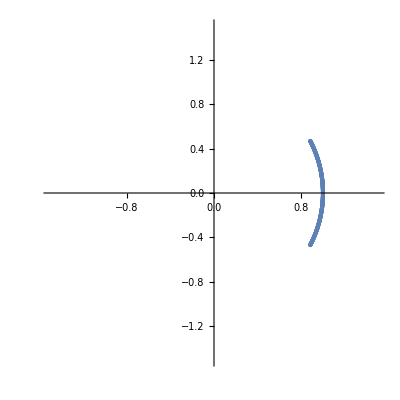

```mathematica
(*CN*)
evals = Eigenvalues[N[MCN]];
realEvals = Re[evals];
imagEvals = Im[evals];
(*combinedEvals = Transpose[{realEvals,imagEvals}];*)
ListPlot[Transpose[{realEvals,imagEvals}],PlotRange->{{-1.5,1.5},{-1.5,1.5}}, AspectRatio->1]
```

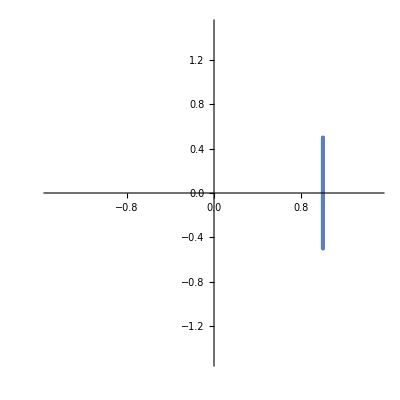

```mathematica
(*Euler*)
evalsEuler = Eigenvalues[N[MEuler]];
realEvalsEuler = Re[evalsEuler];
imagEvalsEuler = Im[evalsEuler];
ListPlot[Transpose[{realEvalsEuler,imagEvalsEuler}],PlotRange->{{-1.5,1.5},{-1.5,1.5}}, AspectRatio->1]
```

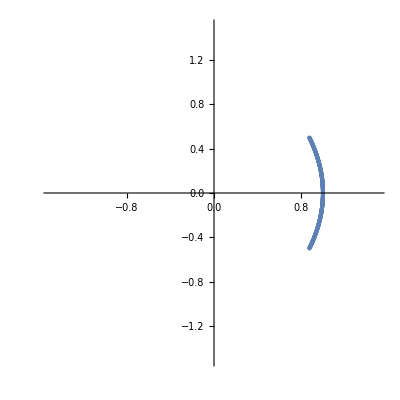

```mathematica
(*RK2*)
evalsRK2 = Eigenvalues[N[MRK2]];
realEvalsRK2 = Re[evalsRK2];
imagEvalsRK2 = Im[evalsRK2];
ListPlot[Transpose[{realEvalsRK2,imagEvalsRK2}],PlotRange->{{-1.5,1.5},{-1.5,1.5}}, AspectRatio->1]
```

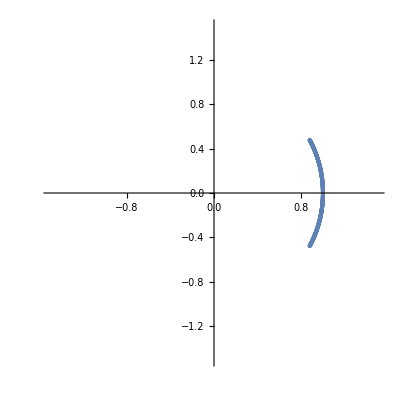

```mathematica
(*RK4*)
evalsRK4 = Eigenvalues[N[MRK4]];
realEvalsRK4 = Re[evalsRK4];
imagEvalsRK4 = Im[evalsRK4];
ListPlot[Transpose[{realEvalsRK4,imagEvalsRK4}],PlotRange->{{-1.5,1.5},{-1.5,1.5}}, AspectRatio->1]
```

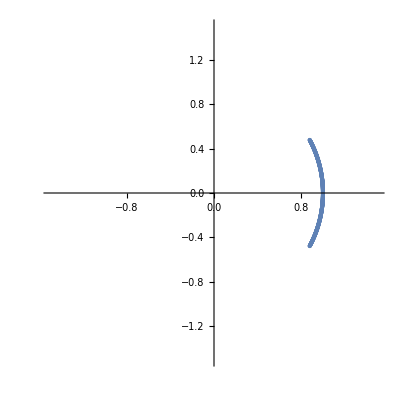

```mathematica
(*New Method*)
evalsN = Eigenvalues[N[MN]];
realEvalsN= Re[evalsN];
imagEvalsN = Im[evalsN];
ListPlot[{Transpose[{realEvalsN,imagEvalsN}]},PlotRange->{{-1.5,1.5},{-1.5,1.5}}, AspectRatio->1]
```

```mathematica
(************************************************************************************************************************)
```

```mathematica
(*Energy*)
```

```mathematica
(************************************************************************************************************************)
```

```mathematica
(*CN*)
FCN = N[Table[0,{i,1,Nt},{j,1,Nx}],32];
FCN = N[FCN,32];
intCN = N[Table[0,{i,1,Length[FCN[[All,1]]]}],32];
intCN = N[intCN,32];
Do[
FCN[[i]] = N[(D1.UCN[[i,All]])^2,32];

intCN[[i]] = N[(2π)/Nx Total[FCN[[i,All]]],32]
,{i,1,Length[FCN[[All,1]]]}];
intCN = N[intCN,32];
(*ListPlot[{Transpose[{T,intCN}]},PlotRange->{All,{0,8}},Joined->True]*)
```

```mathematica
(*Euler*)
FEuler = Table[0,{i,1,Nt},{j,1,Nx}];
intEuler = Table[0,{i,1,Length[FEuler[[All,1]]]}];
Do[
FEuler[[i]] = (D1.UEuler[[i,All]])^2;

intEuler[[i]] = (2π)/Nx Total[FEuler[[i,All]]]
,{i,1,Length[FEuler[[All,1]]]}];
(*ListPlot[{Transpose[{T,intEuler}]},PlotRange->{All,{0,8}},Joined->True]*)
```

```mathematica
(*RK2*)
FRK2= N[Table[0,{i,1,Nt},{j,1,Nx}]32];
FRK2 = N[FRK2,32];
intRK2 = N[Table[0,{i,1,Length[FRK2[[All,1]]]}],32];
intRK2 = N[intRK2,32];
Do[
FRK2[[i]] = N[(D1.URK2[[i,All]])^2,32];

intRK2[[i]] = N[(2π)/Nx Total[FRK2[[i,All]]],32]
,{i,1,Length[FRK2[[All,1]]]}];
intRK2 = N[intRK2,32];
(*ListPlot[{Transpose[{T,intRK2}]},PlotRange->{All,{0,8}},Joined->True]*)
```

```mathematica
(*RK4*)
FRK4= N[Table[0,{i,1,Nt},{j,1,Nx}],32];
FRK4 = N[FRK4,32];
intRK4 = N[Table[0,{i,1,Length[FRK4[[All,1]]]}],32];
intRK4 = N[intRK4,32];
Do[
FRK4[[i]] = N[(D1.URK4[[i,All]])^2,32];

intRK4[[i]] = N[(2π)/Nx Total[FRK4[[i,All]]],32]
,{i,1,Length[FRK4[[All,1]]]}];
intRK4 = N[intRK4,32];
(*ListPlot[{Transpose[{T,intRK4}]},PlotRange->{All,{0,8}},Joined->True]*)
```

```mathematica
(*LD4*)
FN = N[Table[0,{i,1,Nt},{j,1,Nx}],32];
FN = N[FN,32];
intN = N[Table[0,{i,1,Length[FN[[All,1]]]}],32];
intN = N[intN,32];
Do[
FN[[i]] = N[(D1.UN[[i,All]])^2,32];

intN[[i]] = N[(2π)/Nx Total[FN[[i,All]]],32]
,{i,1,Length[FN[[All,1]]]}];
intN = N[intN,32];
(*ListPlot[{Transpose[{T,intN}]},PlotRange->{All,{0,8}},Joined->True]*)
```

```mathematica
(*Exact*)
F = f[X];
F' = f'[X];
fexact[t_,x_] = ⅇ^(- 8((x-t)-π)^2);
(*fexact[t_,x_] = ⅇ^(- 4((x-t)-π)^2);
fexact[t_,x_] = ⅇ^(- 4((((x-xi)*((2*Pi))/(xf-xi))-t)-π)^2);*)
(*fexact[t_,x_] = ⅇ^(-4 (-π+1/50 π (50+(x - t)))^2);*)
(*fexact[t_,x_]=fexact[t,(x-xi)*((2*Pi))/(xf-xi)];*)
Uexact = Table[fexact[T[[i]],X[[j]]],{i,1,Nt},{j,1,Nx}];
FEnergy = Table[0,{i,1,Nt},{j,1,Nx}];
intEnergy = Table[0,{i,1,Length[FEnergy[[All,1]]]}];
Do[
FEnergy[[i]] = (F')^2;

intEnergy[[i]] = (2*Pi)/Nx Total[FEnergy[[i,All]]];
,{i,1,Length[FEnergy[[All,1]]]}];
(*ListPlot[{Transpose[{T,intEnergy}]},Joined->True]*)
```

```mathematica
energyErrorLD2 = N[Abs[intCN - intCN[[1]]],32];
energyErrorLD4 = N[Abs[intN - intN[[1]]],32];
energyErrorRK2 = N[Abs[intRK2 - intRK2[[1]]],32];
energyErrorRK4 = N[Abs[intRK4 - intRK4[[1]]],32];
```

```mathematica
(*D1.UCN[[1,All]] - F'*)
```

```mathematica
(*LD2 Pseudospectral Energy Error*)
(*ListLinePlot[Transpose[{T,energyErrorLD2}], PlotRange->Full]*)
```

```mathematica
(*LD4 Pseudospectral Energy Error*)
(*ListLinePlot[Transpose[{T,energyErrorLD4}], PlotRange->Full]*)
```

```mathematica
(*RK2 Pseudospectral Energy Error*)
(*ListLinePlot[Transpose[{T,energyErrorRK2}], PlotRange->Full]*)
```

```mathematica
(*RK4 Pseudospectral Energy Error*)
(*ListLinePlot[Transpose[{T,energyErrorRK4}], PlotRange->Full]*)
```

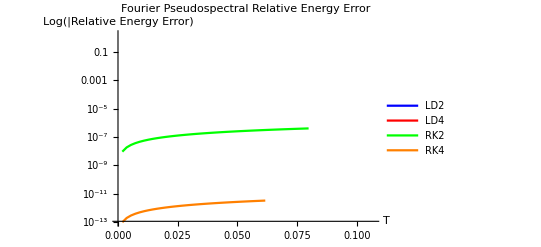

```mathematica
ListLogPlot[{Transpose[{T,energyErrorLD2}], Transpose[{T,energyErrorLD4}], Transpose[{T,energyErrorRK2}], Transpose[{T,energyErrorRK4}]},PlotStyle->{Blue, Red,Green, Orange},PlotLegends->{"LD2","LD4","RK2","RK4"},AxesLabel->{"T","Log(|Relative Energy Error)"},PlotLabel->"Fourier Pseudospectral Relative Energy Error",PlotRange->{{ti,tf},{0,Max[energyErrorRK4]}},Joined->True]
```

```mathematica
(*ListLinePlot[{Transpose[{T,energyErrorLD2}], Transpose[{T,energyErrorLD4}], Transpose[{T,energyErrorRK2}], Transpose[{T,energyErrorRK4}]},PlotRange->{{ti,tf},{0,Max[energyErrorLD2]}}]*)
```

```mathematica
(*exportData=Flatten/@Transpose[{T,energyErrorLD2, energyErrorLD4, energyErrorRK2, energyErrorRK4}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\Energy_Error_Pseudospectral.dat",exportData,"Table"];*)
```

```mathematica
(*exportDataRK4Stable=Flatten/@Transpose[{T,intRK4}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\FDM_RK4_Stable_Energy.dat",exportDataRK4Stable,"Table"];*)
```

```mathematica
(*L1 Error*)
```

```mathematica
(*Uexact = Table[fexact[T[[i]],X[[j]]],{i,1,Nt},{j,1,Nx}];
Uexact = N[Uexact];
Uexact = Chop[N[Uexact], 10^(-307)];*)
(*Map back to original grid*)
(*Do[
Uexact[[i,All]] = xi + ((Uexact[[i,All]])*((xf-xi)/(2*Pi)))
,{i,1,Length[Uexact]}]*)
(*fexact[t_,x_] = ⅇ^(- 4((x-t)-π)^2);
Uexact = Table[fexact[T[[i]],X[[j]]],{i,1,Nt},{j,1,Nx}];*)
```

```mathematica
UN[[100,All]]
```

{0``-15.699580460018403,0``-15.699580460018142,0``-15.699580460017916,0``-15.699580460017685,0``-15.699580460017506,0``-15.699580460017328,0``-15.699580460017179,0``-15.699580460017055,0``-15.699580460016946,0``-15.699580460016865,0``-15.699580460016781,0``-15.69958046001675,0``-15.69958046001671,0``-15.699580460016707,0``-15.699580460016723,0``-15.69958046001674,0``-15.69958046001681,0``-15.699580460016866,0``-15.699580460016978,0``-15.699580460017074,0``-15.699580460017232,0``-15.699580460017351,0``-15.699580460017525,0``-15.699580460017742,0``-15.699580460017938,0``-15.699580460018172,0``-15.699580460018433,0``-15.699580460018732,0``-15.699580460019005,0``-15.699580460019314,0``-15.699580460019662,0``-15.699580460020007,0``-15.69958046002038,0``-15.699580460020773,0``-15.699580460021194,0``-15.69958046002163,0``-15.69958046002208,0``-15.699580460022553,0``-15.699580460023052,0``-15.699580460023569,0``-15.699580460024084,0``-15.699580460024642,0``-15.69958046002521,0``-15.699580460025803,0``-15.699580460026421,0``-15.699580460027043,0``-15.699580460027692,0``-15.699580460028349,0``-15.69958046002904,0``-15.699580460029743,0``-15.699580460030464,0``-15.699580460031207,0``-15.699580460031976,0``-15.69958046003274,0``-15.699580460033529,0``-15.699580460034369,0``-15.699580460035175,0``-15.699580460036032,0``-15.699580460036895,0``-15.69958046003778,0``-15.699580460038689,0``-15.699580460039607,0``-15.699580460040544,0``-15.699580460041497,0``-15.699580460042455,0``-15.69958046004346,0``-15.69958046004446,0``-15.699580460045476,0``-15.699580460046528,0``-15.699580460047557,0``-15.699580460048645,0``-15.699580460049729,0``-15.699580460050841,0``-15.699580460051951,0``-15.699580460053095,0``-15.699580460054236,0``-15.69958046005541,0``-15.6995804600566,0``-15.699580460057794,0``-15.699580460058998,0``-15.699580460060234,0``-15.699580460061478,0``-15.699580460062725,0``-15.699580460063999,0``-15.69958046006529,0``-15.699580460066585,0``-15.699580460067908,0``-15.699580460069235,0``-15.69958046007056,0``-15.699580460071912,0``-15.69958046007329,0``-15.699580460074646,0``-15.699580460076032,0``-15.699580460077442,0``-15.699580460078861,0``-15.699580460080291,0``-15.699580460081734,0``-15.699580460083189,0``-15.69958046008465,0``-15.699580460086109,0``-15.699580460087619,0``-15.699580460089093,0``-15.699580460090614,0``-15.699580460092129,0``-15.699580460093676,0``-15.69958046009521,0``-15.699580460096774,0``-15.699580460098321,0``-15.699580460099883,0``-15.699580460101455,0``-15.699580460103055,0``-15.699580460104647,0``-15.699580460106269,0``-15.699580460107871,0``-15.699580460109496,0``-15.699580460111136,0``-15.69958046011278,0``-15.69958046011441,0``-15.699580460116081,0``-15.699580460117744,0``-15.699580460119419,0``-15.699580460121092,0``-15.699580460122768,0``-15.699580460124459,0``-15.699580460126157,0``-15.699580460127871,0``-15.699580460129578,0``-15.699580460131301,0``-15.699580460133006,0``-15.699580460134742,0``-15.699580460136472,0``-15.699580460138208,0``-15.69958046013994,0``-15.699580460141679,0``-15.69958046014343,0``-15.69958046014519,0``-15.699580460146942,0``-15.699580460148704,0``-15.69958046015047,0``-15.69958046015222,0``-15.69958046015401,0``-15.699580460155767,0``-15.699580460157533,0``-15.699580460159307,0``-15.699580460161096,0``-15.69958046016287,0``-15.699580460164666,0``-15.699580460166427,0``-15.699580460168209,0``-15.699580460169974,0``-15.699580460171767,0``-15.699580460173554,0``-15.699580460175362,0``-15.699580460177119,0``-15.699580460178915,0``-15.699580460180686,0``-15.699580460182474,0``-15.699580460184247,0``-15.699580460186029,0``-15.699580460187793,0``-15.699580460189571,0``-15.699580460191337,0``-15.699580460193106,0``-15.699580460194872,0``-15.69958046019664,0``-15.699580460198398,0``-15.699580460200147,0``-15.699580460201911,0``-15.69958046020364,0``-15.699580460205404,0``-15.699580460207137,0``-15.699580460208884,0``-15.69958046021061,0``-15.69958046021233,0``-15.699580460214069,0``-15.699580460215778,0``-15.6995804602175,0``-15.699580460219192,0``-15.6995804602209,0``-15.69958046022259,0``-15.699580460224283,0``-15.699580460225958,0``-15.699580460227637,0``-15.699580460229294,0``-15.69958046023096,0``-15.699580460232607,0``-15.69958046023426,0``-15.699580460235886,0``-15.69958046023752,0``-15.69958046023914,0``-15.69958046024075,0``-15.699580460242348,0``-15.699580460243945,0``-15.699580460245528,0``-15.699580460247105,0``-15.699580460248665,0``-15.69958046025023,0``-15.699580460251763,0``-15.699580460253308,0``-15.699580460254829,0``-15.69958046025634,0``-15.69958046025784,0``-15.699580460259337,0``-15.699580460260828,0``-15.699580460262283,0``-15.699580460263752,0``-15.699580460265175,0``-15.69958046026661,0``-15.699580460268033,0``-15.69958046026943,0``-15.699580460270848,0``-15.699580460272216,0``-15.699580460273594,0``-15.699580460274962,0``-15.699580460276323,0``-15.699580460277636,0``-15.699580460278959,0``-15.699580460280243,0``-15.69958046028154,0``-15.699580460282808,0``-15.69958046028408,0``-15.69958046028533,0``-15.699580460286564,0``-15.699580460287766,0``-15.699580460288988,0``-15.699580460290157,0``-15.699580460291342,0``-15.699580460292495,0``-15.699580460293644,0``-15.699580460294742,0``-15.699580460295868,0``-15.69958046029697,0``-15.699580460298046,0``-15.699580460299092,0``-15.69958046030015,0``-15.699580460301185,0``-15.699580460302183,0``-15.699580460303197,0``-15.699580460304158,0``-15.69958046030513,0``-15.69958046030608,0``-15.699580460307017,0``-15.699580460307894,0``-15.69958046030879,0``-15.699580460309665,0``-15.69958046031051,0``-15.69958046031136,0``-15.699580460312193,0``-15.699580460312994,0``-15.699580460313777,0``-15.699580460314532,0``-15.699580460315289,0``-15.699580460316023,0``-15.699580460316726,0``-15.699580460317408,0``-15.699580460318083,0``-15.699580460318733,0``-15.699580460319376,0``-15.69958046031998,0``-15.699580460320588,0``-15.699580460321165,0``-15.699580460321725,0``-15.699580460322254,0``-15.699580460322771,0``-15.699580460323286,0``-15.699580460323759,0``-15.699580460324219,0``-15.69958046032467,0``-15.699580460325084,0``-15.699580460325498,0``-15.699580460325873,0``-15.69958046032624,0``-15.699580460326581,0``-15.699580460326887,0``-15.699580460327196,0``-15.69958046032748,0``-15.699580460327734,0``-15.699580460327994,0``-15.69958046032821,0``-15.6995804603284,0``-15.699580460328576,0``-15.699580460328741,0``-15.699580460328885,0``-15.699580460329013,0``-15.699580460329106,0``-15.699580460329177,0``-15.699580460329251,0``-15.699580460329281,0``-15.699580460329303,0``-15.699580460329301,0``-15.699580460329276,0``-15.69958046032923,0``-15.699580460329171,0``-15.699580460329082,0``-15.699580460328988,0``-15.699580460328853,0``-15.699580460328724,0``-15.699580460328557,0``-15.699580460328372,0``-15.699580460328173,0``-15.699580460327939,0``-15.699580460327692,0``-15.699580460327436,0``-15.699580460327143,0``-15.699580460326839,0``-15.699580460326514,0``-15.699580460326178,0``-15.699580460325818,0``-15.699580460325414,0``-15.699580460325015,0``-15.699580460324595,0``-15.699580460324151,0``-15.699580460323686,0``-15.699580460323196,0``-15.699580460322693,0``-15.69958046032217,0``-15.69958046032164,0``-15.699580460321071,0``-15.69958046032049,0``-15.69958046031989,0``-15.699580460319265,0``-15.699580460318636,0``-15.699580460317964,0``-15.699580460317303,0``-15.699580460316605,0``-15.6995804603159,0``-15.69958046031516,0``-15.699580460314417,0``-15.699580460313646,0``-15.699580460312855,0``-15.699580460312044,0``-15.699580460311227,0``-15.699580460310388,0``-15.699580460309528,0``-15.699580460308647,0``-15.699580460307773,0``-15.699580460306848,0``-15.699580460305906,0``-15.699580460304958,0``-15.699580460303997,0``-15.699580460303025,0``-15.69958046030203,0``-15.699580460301007,0``-15.699580460299982,0``-15.699580460298925,0``-15.699580460297863,0``-15.699580460296787,0``-15.699580460295676,0``-15.699580460294579,0``-15.699580460293442,0``-15.699580460292283,0``-15.699580460291148,0``-15.699580460289967,0``-15.69958046028879,0``-15.699580460287578,0``-15.699580460286347,0``-15.699580460285121,0``-15.69958046028386,0``-15.69958046028261,0``-15.699580460281329,0``-15.699580460280039,0``-15.699580460278723,0``-15.699580460277405,0``-15.699580460276078,0``-15.699580460274726,0``-15.699580460273376,0``-15.699580460271996,0``-15.699580460270619,0``-15.699580460269216,0``-15.699580460267804,0``-15.699580460266384,0``-15.699580460264952,0``-15.699580460263489,0``-15.699580460262032,0``-15.699580460260563,0``-15.699580460259074,0``-15.69958046025759,0``-15.699580460256078,0``-15.699580460254566,0``-15.699580460253035,0``-15.699580460251502,0``-15.699580460249958,0``-15.699580460248399,0``-15.699580460246835,0``-15.699580460245251,0``-15.699580460243672,0``-15.699580460242077,0``-15.699580460240465,0``-15.69958046023886,0``-15.699580460237243,0``-15.699580460235621,0``-15.699580460233978,0``-15.699580460232323,0``-15.69958046023068,0``-15.699580460229013,0``-15.699580460227345,0``-15.699580460225679,0``-15.699580460223999,0``-15.699580460222304,0``-15.699580460220602,0``-15.699580460218908,0``-15.6995804602172,0``-15.699580460215486,0``-15.699580460213767,0``-15.699580460212047,0``-15.699580460210314,0``-15.699580460208583,0``-15.699580460206848,0``-15.699580460205102,0``-15.69958046020336,0``-15.699580460201597,0``-15.699580460199854,0``-15.699580460198097,0``-15.699580460196335,0``-15.699580460194564,0``-15.699580460192806,0``-15.699580460191045,0``-15.699580460189267,0``-15.699580460187494,0``-15.699580460185718,0``-15.699580460183936,0``-15.699580460182167,0``-15.69958046018038,0``-15.699580460178595,0``-15.699580460176813,0``-15.69958046017502,0``-15.699580460173255,0``-15.699580460171473,0``-15.699580460169683,0``-15.699580460167915,0``-15.699580460166125,0``-15.699580460164347,0``-15.699580460162572,0``-15.699580460160783,0``-15.699580460159018,0``-15.699580460157241,0``-15.699580460155468,0``-15.699580460153697,0``-15.699580460151928,0``-15.699580460150166,0``-15.699580460148416,0``-15.699580460146635,0``-15.699580460144892,0``-15.699580460143137,0``-15.699580460141393,0``-15.699580460139646,0``-15.699580460137911,0``-15.699580460136177,0``-15.699580460134447,0``-15.699580460132717,0``-15.699580460131003,0``-15.699580460129285,0``-15.699580460127574,0``-15.69958046012587,0``-15.69958046012418,0``-15.6995804601225,0``-15.699580460120805,0``-15.699580460119131,0``-15.699580460117465,0``-15.699580460115799,0``-15.69958046011415,0``-15.699580460112498,0``-15.699580460110868,0``-15.699580460109226,0``-15.69958046010761,0``-15.699580460105988,0``-15.699580460104386,0``-15.69958046010279,0``-15.699580460101199,0``-15.699580460099618,0``-15.699580460098057,0``-15.699580460096497,0``-15.699580460094946,0``-15.699580460093406,0``-15.69958046009188,0``-15.699580460090358,0``-15.699580460088852,0``-15.699580460087356,0``-15.699580460085869,0``-15.699580460084398,0``-15.699580460082942,0``-15.699580460081481,0``-15.699580460080046,0``-15.699580460078622,0``-15.699580460077206,0``-15.699580460075797,0``-15.699580460074413,0``-15.699580460073038,0``-15.69958046007167,0``-15.699580460070319,0``-15.69958046006899,0``-15.699580460067663,0``-15.69958046006635,0``-15.699580460065064,0``-15.699580460063773,0``-15.699580460062514,0``-15.699580460061254,0``-15.699580460060016,0``-15.699580460058801,0``-15.699580460057588,0``-15.699580460056396,0``-15.699580460055211,0``-15.699580460054046,0``-15.699580460052893,0``-15.699580460051767,0``-15.699580460050646,0``-15.699580460049543,0``-15.699580460048466,0``-15.699580460047398,0``-15.699580460046343,0``-15.699580460045308,0``-15.699580460044286,0``-15.699580460043292,0``-15.6995804600423,0``-15.699580460041334,0``-15.69958046004038,0``-15.699580460039448,0``-15.699580460038527,0``-15.699580460037621,0``-15.699580460036746,0``-15.699580460035877,0``-15.699580460035037,0``-15.699580460034205,0``-15.699580460033399,0``-15.699580460032609,0``-15.699580460031836,0``-15.699580460031076,0``-15.69958046003034,0``-15.699580460029622,0``-15.699580460028926,0``-15.699580460028242,0``-15.699580460027581,0``-15.699580460026937,0``-15.69958046002631,0``-15.69958046002571,0``-15.699580460025112,0``-15.69958046002455,0``-15.699580460023999,0``-15.699580460023466,0``-15.699580460022956,0``-15.69958046002247,0``-15.699580460021998,0``-15.699580460021549,0``-15.699580460021126,0``-15.699580460020709,0``-15.69958046002032,0``-15.699580460019947,0``-15.699580460019599,0``-15.699580460019263,0``-15.699580460018959,0``-15.699580460018666}

```mathematica
(*LD2*)
abserrLD2 = Abs[UCN-Uexact];
errorLD2 = Table[0,{i,1,Length[abserrLD2]}];
maxabserrLD2 = Table[0,{i,1,Length[abserrLD2]}];
Do[
abserrLD2[[i,All]] = UCN[[i,All]] - Uexact[[i,All]];
errorLD2[[i]] = Norm[abserrLD2[[i,All]], 1] * deltax;
maxabserrLD2[[i]] = Max[abserrLD2[[i,All]]];
,{i,1,Length[errorLD2]}
];
(*ListLinePlot[Transpose[{T,errorLD2}],PlotRange->All]*)
```

```mathematica
(*RK2*)
abserrRK2 = Abs[URK2-Uexact];
maxabserrRK2 = Max[abserrRK2]
errorRK2 = Table[0,{i,1,Length[abserrRK2]}];
Do[
errorRK2[[i]] = Norm[abserrRK2[[i,All]], 1] * deltax;
,{i,1,Length[errorRK2]}
];
(*ListLinePlot[Transpose[{T,errorRK2}]]*)
```

1.

```mathematica
(*LD4*)
abserrLD4 = Abs[UN-Uexact];
maxabserrLD4 = Max[abserrLD4]
errorLD4 = Table[0,{i,1,Length[abserrLD4]}];
Do[
errorLD4[[i]] = Norm[abserrLD4[[i,All]], 1] * deltax;
,{i,1,Length[errorLD4]}
];
(*ListLinePlot[Transpose[{T,errorLD4}]]*)
```

0.04

```mathematica
(*RK4*)
abserrRK4 = Abs[URK4-Uexact];
maxabserrRK4 = Max[abserrRK4]
errorRK4 = Table[0,{i,1,Length[abserrRK4]}];
Do[
errorRK4[[i]] = Norm[abserrRK4[[i,All]], 1] * deltax;
,{i,1,Length[errorRK4]}
];
(*ListLinePlot[Transpose[{T,errorRK4}],PlotRange->All]*)
```

0.7

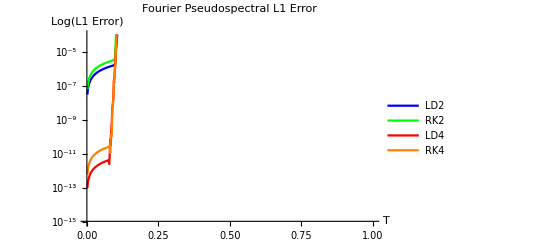

```mathematica
ListLogPlot[{Transpose[{T,errorLD2}], Transpose[{T,errorRK2}], Transpose[{T,errorLD4}], Transpose[{T,errorRK4}]},PlotRange->{{ti,tf},{1*10^-15,1*10^-4}}, PlotStyle->{Blue,Green,Red,Orange},PlotLegends->{"LD2","RK2","LD4","RK4"},AxesLabel->{"T","Log(L1 Error)" },PlotLabel->"Fourier Pseudospectral L1 Error", Joined->True]
```

```mathematica
(*exportData=Flatten/@Transpose[{T,errorLD2, errorLD4, errorRK2, errorRK4}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\Error_PS.dat",exportData,"Table"];*)
```

```mathematica
(*Animate[ListPlot[Table[UN[[n+1, m+1]], {m,0,Nx  - 1}], PlotRange->{All,{0,2}}], {n,0,Nt - 1,1}]*)
```

```mathematica
aniLD2 = Animate[ListLinePlot[{Transpose[{X,UCN[[n]]}],Transpose[{X,Uexact[[n]]}]},PlotStyle -> {{Orange,Dashed},{Blue,Opacity[0.5]}},PlotRange->{{0,2*Pi},{0,1}}], {n,1,Nt ,1} ]
```

```mathematica
Animate[ListLinePlot[Transpose[{X,(UCN[[n]] - Uexact[[n]])}],PlotRange->{{xi,xf},{-.00001,.00001}}], {n,1,Nt ,1} ]
```

```mathematica
(********************************************************************************************************************)
(*Start/Final*)

(*LD2*)
LD2start = UCN[[1]];
LD2startErr = UCN[[1]] - Uexact[[1]];
LD2end = Last[UCN];
LD2endErr = Last[UCN] - Last[Uexact];

(*LD4*)
LD4start = UN[[1]];
LD4startErr = UN[[1]] - Uexact[[1]];
LD4end = Last[UN];
LD4endErr = Last[UN] - Last[Uexact];

(*RK2*)
RK2start = URK2[[1]];
RK2startErr = URK2[[1]] - Uexact[[1]];
RK2end = Last[URK2];
RK2endErr = Last[URK2] - Last[Uexact];

(*RK4*)
RK4start = URK4[[1]];
RK4startErr = URK4[[1]] - Uexact[[1]];
RK4end = Last[URK4];
RK4endErr = Last[URK4] - Last[Uexact];

(*exportData=Flatten/@Transpose[{X,LD2start, LD2startErr, LD2end, LD2endErr,RK2start, RK2startErr, RK2end, RK2endErr, LD4start, LD4startErr, LD4end, LD4endErr,RK4start, RK4startErr, RK4end, RK4endErr}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\start_final_PS.dat",exportData,"Table"];*)
```